# Penalization Review

Penalization refers to adding a (probably positive) penalty term to an objective function f to enforce (or maybe just encourage) satisfaction of a constraint.  There are a few broad categories.  We are going to demonstrate the strategies on our simple quadratic 
	f(x)=0.5x.A.x+g.x
where A is an n×n symmetric but not necessarily SPD matrix subject to a set of linear constraints
	B_i.x+b_i≥0  for i=1:m
Since these are inequality constraints we do NOT know that the m×n matrix
	B=(B_1
B_2
⋮
B_m)
is short and fat! There can be many more inequality constraints than variables!  We are going to look at things in 1 and 2D.

We want to convert constrained problems 
	argmin_(x∈Ω)f(x)
into “equivalent” unconstrained problem
	argmin g(x)
by adding a penalty term p(x) to f(x) i.e. 
	g(x)=f(x)+p(x) .
We would like the penalty term to be:
	— Easy to deal with
	— Smooth
	— Not change the minimum too much
For the constraint c>0 our prototypes are shown below.

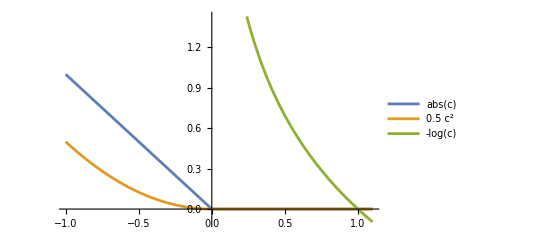

```mathematica
Plot[{If[c<0,-c,0],If[c<0,0.5 c^2,0],-Log[c]},{c,-1,1.1},
PlotLegends->{"abs(c)","0.5 c^2","-log(c)"}]
```

#### Ex 1D:

All intervals a≤x≤b look the same. We are going to look at 0≤x≤100. We want to convert the constrained problem 
	argmin_(0≤x≤100)f(x)
into an “equivalent” unconstrained problem
	argmin g(x)
by adding a penalization

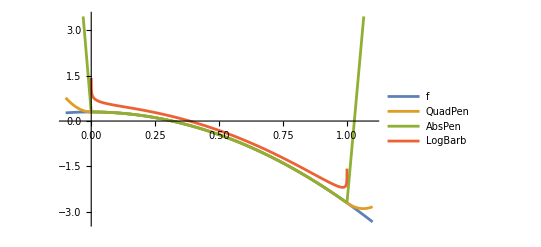

```mathematica
Clear[f,p1,p2,b]
f[x_]:=0.3-3 x^2
QuadPen[c_]:= If[c<0,0.5 c^2,0]
AbsPen[c_]:= If[c<0,-c,0]
LogBar[c_]:= If[c<0,∞,-Log[c]]

{μ,ϵ}={100,0.1};
Plot[{f[x],f[x]+μ (QuadPen[x]+QuadPen[1-x]),
f[x]+μ (AbsPen[x]+AbsPen[1-x]),f[x]+ϵ (LogBar[x]+LogBar[1-x])},{x,-0.1,1.1},
PlotLegends->{"f","QuadPen","AbsPen","LogBarb"}]
```

#### Ex 2D:

```mathematica
{n,m}={2,5};
f[x_]:=Sin[x⟦1⟧x⟦2⟧-Cos[3x⟦1⟧+x⟦2⟧]-x⟦2⟧]
p[t_]:={Cos[2π(t-0.15)],3 Sin[2 π (t+0.2)]};
normal[t_]:={1,-1}*Reverse[p'[t]]
B=Table[ normal[i/m],{i,1,m}];b=Table[-normal[i/m].p[i/m],{i,1,m}];
{μ,ϵ}={1,0.01};
TabView[{
"cons"->Show[
RegionPlot[Apply[And,Table[B⟦i⟧.{x1,x2}+b⟦i⟧>0,{i,1,m}]],
{x1,-3,3},{x2,-3,3}],
ParametricPlot[p[t],{t,0,1},PlotStyle->Red],
Epilog->{PointSize[0.02],Point[Table[p[i/m],{i,1,m}]]}
],
"3D"->Plot3D[f[{x1,x2}],{x1,-3,3},{x2,-3,3},
PlotLegends->Automatic,
PlotRange->{-2,2},
RegionFunction->Function[{x1,x2},Min[B.{x1,x2}+b]]],
"3D Quad Penalty"->Plot3D[
f[{x1,x2}]+μ Sum[QuadPen[B⟦i⟧.{x1,x2}+b⟦i⟧],{i,1,m}],
{x1,-3,3},{x2,-3,3},
Exclusions->None,
PlotRange->{-2,2}],
"3D Log Barrier"->Plot3D[
f[{x1,x2}]+ϵ Sum[LogBar[B⟦i⟧.{x1,x2}+b⟦i⟧],{i,1,m}],
{x1,-3,3},{x2,-3,3},
PlotRange->{-2,2},
PlotPoints->200,
Exclusions->None]
},2]
```

1234

Summary 
A) Quadratic penalization is smooth but will have computed points that are infeasible. It will also have increasingly badly conditioned linear algebra as the penalization parameter is increased.
B) Abs value penalization is NOT smooth. As the penalization parameter is increased computed point hit the edge of the feasible region. But (and it is a huge but) our techniques do not work on non-smooth problems.
C) Log barrier is smooth and computed points need to be in the feasible region interior. Computed points approach the border of the feasible set as the barrier parameter ϵ is decreased. It is possible to exploit the simple explicit gradient 
	∇_x (∑_(k=1)^m LogBar[c_i(x)])=-∑_(k=1)^m 1/(c_i(x))∇c_i(x)
to partially separate the constraint and cost function computations.   This is the basis of Interior Point Methods.

## KKT Reminder

The equations that give solutions to 
	min_(x∈Ω) f(x)
where the feasible set is 
	Ω={x∈ℝ^n withc_i(x)≥0 | for i∈ℐ }
are in terms of the Lagrangian ℒ(x,λ)=f(x)-∑_(i∈ℐ) λ_i c_i(x) are

∇_x ℒ(x,λ)=∇f(x)-∑_(i∈ℐ) λ_i∇c_i(x)=0_n

c_i(x)≥0 and λ_i≥0 for i∈ℐ 	“satisfies inequality constraints with positive Lagrange multipliers”

λ_i c_i(x)=0 for i∈ℐ		“inactive constraints have zero multipliers”

Our target is to find an iteration that produces a sequence of feasible points,  reduces f(x) at each step, and converges to a KKT point.

#### For i∈ℐ we need λ_i c_i=0 “Complementary Slackness” Relaxing “Complementary Slackness”

The sets λ c=σ look pretty close to the set λ c=0 provided σ is small.  Relaxing complementary slacknes means replacing λ c=0 with λ c=σ and letting σ↘0.

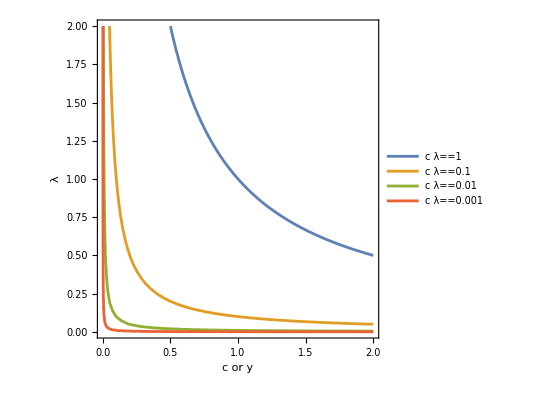

```mathematica
ContourPlot[{λ c ==1,λ c ==0.1,λ c ==0.01,λ c == 0.001},
{c,0,2},{λ,0,2},
FrameLabel->{"c or y","λ"},
PlotLegends->"Expressions"]
```

The connection with the log barrier formulation is that if λ c=σ the gradient 
	∇_x (-log(c))=-1/c∇_x c = -σ λ ∇_x c
which is quadratic.  Since Newton’s method is well suited to quadratic terms like this the log-barrier formulation generates practical algorithms.  These algorithms can be developed from log-barrier formulations but they are usually developed in linear algebraic language.

## Interior Point Notation for 16.6 p480 LCQP - Linearly Constrained Quadratic Program

For no apparent reason our book has changed notation!
	min_x 0.5 x.G.x+c.x
subject to 
	A.x≥b
where G=Gᵀ is an n×n matrix, b is an n vector, A is an m×n vector, and b is an m vector. We (and the book) are going to stick with this.  The KKT equations simplify to

G.x+c-Aᵀ.λ=0  	from ∇_x ℒ(x,λ)=∇f(x)-∑_(i∈ℐ) λ_i∇c_i(x)=0_n

A[i,:].x≥b_i for 1≤i≤m	“constraints satisfied”

λ_i≥0 for 1≤i≤m 	“non-negative Lagrange multipliers”

λ_i c_i(x)=0 for 1≤i≤m	“inactive constraints have zero multipliers”

It is standard to get rid of the inequalities by creating an m vector of positive slack variables
	y=A.x-b≥0_m
It is standard to write all of this as vectors in which case we get the system

G.x+c-Aᵀ.λ=0_n

A.x-y-b=0_m

λ≥0_m	“non-negative Lagrange multipliers”

y≥0_m	“non-negative slack variables”

y_i λ_i=0	“inactive constraints are off

Our target is to find an iteration 
	(x_(k+1),y_(k+1),λ_(k+1))⟶ (x_(k+1),y_(k+1),λ_(k+1))
that satisfies the first four of these conditions and has “complementary measure” 
	μ_k=(y_k.λ_k)/m⟶0
going to zero as k→∞. In words, it produces feasible points with appropriate multipliers that approach the “complementary slackness” condition in the KKT equations.  If we can do this then we can eventually satisfy the KKT conditions as accurately as we want. In other words, we can find KKT points.

## Perturbed Interior Point Equations LCQP §16.6 p481

Our target is a stack of “almost linear algebra” equations.  Look at
	F((x,y,λ);σ,μ)=(G.x-Aᵀ.λ+c
A.x-y-b
𝒴.Λ(.1)_m-σ μ 1_m)
where 
	𝒴=(y_1 | 0 | ⋯ |   | 0
0 | y_2 |   |   | ⋮
⋮ |   | ⋱ |   |  
  |   |   | y_(m-1) | 0
0 | ⋯ |   | 0 | y_m), Λ=(λ_1 | 0 | ⋯ |   | 0
0 | λ_2 |   |   | ⋮
⋮ |   | ⋱ |   |  
  |   |   | λ_(m-1) | 0
0 | ⋯ |   | 0 | λ_m) and 1_m=(1
1
⋮
 
1).
for fixed σ and μ we can apply Newton’s method to the slightly nonlinear function F:ℝ^(n+m+m)→ℝ^(n+m+m) to start solving F((x,y,λ):σ,μ)=0_(n+2m).  Writing z=(x,y,λ)∈ℝ^(n+2m) for the concatenated vector we have
	∇_z F=(G | 0 | -Aᵀ
A | -I | 0
0 | Λ | 𝒴) .
One step of a Newton iteration that would converge with a decent initial condition would be
	z_(n+1)=z_n+Δz
where Δz=(Δx,Δy,Δz) satisfies 
(M)	(G | 0 | -Aᵀ
A | -I | 0
0 | Λ | 𝒴)(Δx
Δy
Δλ)=(-(G.x-Aᵀ.λ+c)
-(A.x-y-b)
-Λ.𝒴(.1)_n+σ μ 1_n).
The problem is that that y_n+Δy and λ_n+Δλ may not have all positive entries even though y_n and λ_n do. The standard solution is to restrict the step by finding an α<1 so that 
	z_(n+1)=(x_(n+1),y_(n+1)^+,λ_(n+1^+))=(x_n,y_n,λ_n)+α(Δx,Δy,Δy)
is feasible i.e. y_(n+1)^+ and λ_(n+1)^+ have all positive entries.

The discussion of efficiently solving equation (M) focuses on G SPD in which case this is a Linearly Constrained Convex Quadratic Program.

I am going to implement Algorithm 16.4 on page 484.